```mathematica
Clear["Global`*"]
```

This .nb contains the code used to generate Figure 2 in arXiv:2511.16196

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor}"}];
tex[x_]:=MaTeX[x,Magnification->1.2,FontSize->16];
fticks1[min_,max_]:=Table[If[IntegerQ[i],{10.^i,10.^i,{.02,0}},{(9.(i-Floor[i])+1)10.^Floor[i],"",{.01,0}}],{i,Floor[Log10[min]],Ceiling[Log10[max]],1/9}]
fticks1p[min_,max_]:=Table[If[EvenQ[i],{10.^i,10.^i,{.01,0}},{10.^i,"",{.01,0}}],{i,Floor[Log10[min]],Ceiling[Log10[max]],1}];
fticks2[min_,max_]:=Table[{10.^i,"",{.01,0}},{i,Floor[Log10[min]],Ceiling[Log10[max]],1}];
fticks1x[min_,max_]:=Table[If[IntegerQ[i],{10.^i,"",{.02,0}},{(9.(i-Floor[i])+1)10.^Floor[i],"",{.01,0}}],{i,Floor[Log10[min]],Ceiling[Log10[max]],1/9}]


repticklabels={0.000000000000000000000001->"10^-24",0.00000000000000000000001->"10^-23",0.0000000000000000000001->"10^-22",0.000000000000000000001->"10^-21",0.00000000000000000001->"10^-20",0.0000000000000000001->"10^-19",0.000000000000000001->"10^-18",0.00000000000000001->"10^-17",0.0000000000000001->"10^-16",0.000000000000001->"10^-15",0.00000000000001->"10^-14",0.0000000000001->"10^-13",0.000000000001->"10^-12",0.00000000001->"10^-11",0.0000000001->"10^-10",0.000000001->"10^-9",0.00000001->"10^-6",0.0000001->"10^-7",0.000001->"10^-6",0.00001->"10^-5",0.0001->"10^-4",0.001->"10^-3",
0.01->0.01,0.1->0.1,1.->1,10.->10,100.->100,1000.->"10^3",10000.->"10^4",100000.->"10^5",1000000.->"10^6",10000000.->"10^7",100000000.->"10^8",1000000000.->"10^9",1.*10^10->"10^10",1.*10^11->"10^11",1.*10^12->"10^12",1.*10^13->"10^13",1.*10^14->"10^14",1000000000000000.->"10^15",10000000000000000.->"10^16",1.*10^17->"10^17",1.*10^18->"10^18",10000000000000000000.->"10^19",100000000000000000000.->"10^20",1000000000000000000000.->"10^21"};
```

```mathematica
v=174*10^9;(*TeV*)
(*quark sector*)
ubf=2.54*10^-6;
cbf=1.37*10^-3;
tbf=0.428;
uer=0.86*10^-6;
cer=0.04*10^-3;
ter=0.003;

dbf=6.56*10^-6;
sbf=1.24*10^-4;
bbf=5.7*10^-3;
der=0.65*10^-6;
ser=0.06*10^-4;
ber=0.05*10^-3;

ebf=2.70341*10^-6;
μbf=5.70705*10^-4;
τbf=9.70200*10^-3;
eer=0.0270*10^-6;
μer=0.0570*10^-4;
τer=0.0970*10^-3;

qθ12=0.22739;
qθ23=4.858*10^-2;
qθ13=4.202*10^-3;
qδcp=1.207;
qθ12er=0.0006;
qθ23er=0.06*10^-2;
qθ13er=0.13*10^-3;
qδcper=0.054;

(*leptons*)
ebf=2.70341*10^-6;
μbf=5.70705*10^-4;
τbf=9.70200*10^-3;

eer=0.0270*10^-6;
μer=0.0570*10^-4;
τer=0.0970*10^-3;
```

```mathematica
ν1Oct=<|"Δms21"->7.498*10^-5,"Δms31"->2.513*10^-3,"Δms21er"->0.116*10^-5,"Δms31er"->1/2*(0.021+0.019)*10^-3,
"vθ12"->0.309,"vθ23"->0.470,"vθ13"->0.02215,
"vθ12er"->0.009,"vθ23er"->1/2*(0.013+0.017) ,"vθ13er"->1/2*(0.00056+0.00058)|>;


ν2Oct=<|"Δms21"->7.498*10^-5,"Δms31"->2.534*10^-3,"Δms21er"->0.116*10^-5,"Δms31er"->1/2*(0.023+0.025)*10^-3,
"vθ12"->0.309,"vθ23"->0.561,"vθ13"->0.02195,
"vθ12er"->0.009 ,"vθ23er"->0.5*(0.012+0.015),"vθ13er"->0.5*(0.00054+0.00058) |>;
```

```mathematica
dat11=Map[N,Import[FileNameJoin[{NotebookDirectory[],"Parameters//M1_1st.dat"}],"Table"],{2}];
dat11//Dimensions
dat12=Map[N,Import[FileNameJoin[{NotebookDirectory[],"Parameters//M1_2nd.dat"}],"Table"],{2}];
dat12//Dimensions
dat21=Map[N,Import[FileNameJoin[{NotebookDirectory[],"Parameters//M2_1st.dat"}],"Table"],{2}];
dat21//Dimensions
dat22=Map[N,Import[FileNameJoin[{NotebookDirectory[],"Parameters//M2_2nd.dat"}],"Table"],{2}];
dat22//Dimensions
dat31=Map[N,Import[FileNameJoin[{NotebookDirectory[],"Parameters//M3_1st.dat"}],"Table"],{2}];
dat31//Dimensions
dat32=Map[N,Import[FileNameJoin[{NotebookDirectory[],"Parameters//M3_2nd.dat"}],"Table"],{2}];
dat32//Dimensions
```

{9761,19}

{9709,19}

{8708,19}

{8725,19}

{17616,18}

{15332,18}

```mathematica
M1$Chi2[d11_,d22_,d33_,s11_,s12_,s13_,s22_,s23_,s33_,s1_,s2_,s3_,s4_,s5_,s6_,r1_,r2_,ω_,m0_,νpara_]:=
Module[{yu,yd,ye,yv,h,f,tprs,cprs,uprs,U3,U2,U1,bprs,sprs,dprs,D3,D2,D1,τprs,μprs,eprs,E3,E2,E1,chiu,chid,chie,chiv,chickm,chipmns,m3prs,m2prs,m1prs,V3,V2,V1,mv,Vckm,Vpmns,qt12,qt13,qt23,qdcp,vt12,vt13,vt23,vθ12,vθ13,vθ23,vθ12er,vθ13er,vθ23er,Δms21,Δms31,Δms21er,Δms31er,vdcp,ρ,σ,MN,mcos,me,mee,chit,Dx,S,},
vθ12=νpara["vθ12"];vθ13=νpara["vθ13"];vθ23=νpara["vθ23"];
vθ12er=νpara["vθ12er"];vθ13er=νpara["vθ13er"];vθ23er=νpara["vθ23er"];
Δms21=νpara["Δms21"];Δms31=νpara["Δms31"];
Δms21er=νpara["Δms21er"];Δms31er=νpara["Δms31er"];
Dx=({{d11, 0, 0}, {0, d22, 0}, {0, 0, d33}});S=({{s11*Exp[I*s1], s12*Exp[I*s2], s13*Exp[I*s3]}, {s12*Exp[I*s2], s22*Exp[I*s4], s23*Exp[I*s5]}, {s13*Exp[I*s3], s23*Exp[I*s5], s33*Exp[I*s6]}});
yu=S+Dx;
yd=r2*S+Exp[I*ω]*r1*Dx;
ye=r2*S-3Exp[I*ω]*r1*Dx;
yv=S-3*Dx;
mv=-m0*yv.({{1/d11, 0, 0}, {0, 1/d22, 0}, {0, 0, 1/d33}}).Transpose[yv];
MN=Dx/m0*174^2*10^9;

{{tprs,cprs,uprs},{U3,U2,U1}}=Chop[Eigensystem[yu.ConjugateTranspose[yu]]//N,10^-14];
{{bprs,sprs,dprs},{D3,D2,D1}}=Chop[Eigensystem[yd.ConjugateTranspose[yd]]//N,10^-14];
{{τprs,μprs,eprs},{E3,E2,E1}}=Chop[Eigensystem[ye.ConjugateTranspose[ye]]//N,10^-14];
{{m3prs,m2prs,m1prs},{V3,V2,V1}}=Chop[Eigensystem[mv.ConjugateTranspose[mv]]//N,10^-14];

chiu=(√uprs-ubf)^2/uer^2+(√cprs-cbf)^2/cer^2+(√tprs-tbf)^2/ter^2;
chid=(√dprs-dbf)^2/der^2+(√sprs-sbf)^2/ser^2+(√bprs-bbf)^2/ber^2;
chie=(√eprs-ebf)^2/eer^2+(√μprs-μbf)^2/μer^2+(√τprs-τbf)^2/τer^2;
chiv=(m2prs-m1prs-Δms21)^2/Δms21er^2+(m3prs-m1prs-Δms31)^2/Δms31er^2;
Vckm=ConjugateTranspose[Transpose[Normalize/@{U1,U2,U3}]].Transpose[Normalize/@{D1,D2,D3}];

qt12=ArcTan[Abs[Vckm[[1,2]]]/Abs[Vckm[[1,1]]]];
qt13=ArcSin[Abs[Vckm[[1,3]]]];
qt23=ArcTan[Abs[Vckm[[2,3]]]/Abs[Vckm[[3,3]]]];
qdcp=Arg[(Vckm[[1,1]]*Vckm[[3,3]]*Conjugate[Vckm[[1,3]]]*Conjugate[Vckm[[3,1]]]+Abs[Vckm[[1,1]]*Vckm[[3,3]]*Vckm[[1,3]]]^2/(1-Abs[Vckm[[1,3]]]^2))];
chickm=1/qθ12er^2*(qt12-qθ12)^2+1/qθ13er^2*(qt13-qθ13)^2+1/qθ23er^2*(qt23-qθ23)^2+1/qδcper^2*(qdcp-qδcp)^2;Vpmns=ConjugateTranspose[Transpose[Normalize/@{E1,E2,E3}]].Transpose[Normalize/@{V1,V2,V3}];
mee=Abs[√m1prs*Vpmns[[1,1]]^2+√m2prs*Vpmns[[1,2]]^2+√m3prs*Vpmns[[1,3]]^2];
vt12=ArcTan[Abs[Vpmns[[1,2]]]/Abs[Vpmns[[1,1]]]];
vt13=ArcSin[Abs[Vpmns[[1,3]]]];
vt23=ArcTan[Abs[Vpmns[[2,3]]]/Abs[Vpmns[[3,3]]]];

chipmns=1/vθ12er^2*(Sin[vt12]^2-vθ12)^2+1/vθ13er^2*(Sin[vt13]^2-vθ13)^2+1/vθ23er^2*(Sin[vt23]^2-vθ23)^2;
vdcp=(Vpmns[[1,1]]*Vpmns[[3,3]]*Conjugate[Vpmns[[1,3]]]*Conjugate[Vpmns[[3,1]]]+Abs[Vpmns[[1,1]]*Vpmns[[3,3]]*Vpmns[[1,3]]]^2/(1-Abs[Vpmns[[1,3]]]^2));
chit=(chiu+chid+chie+chiv+chickm+chipmns)/18;

Join[{chit},Diagonal[MN][[{1,2,3}]],{√(m1prs//Abs),mee},{vt23/Pi*180,Mod[Arg[vdcp]/Pi*180,360]}]];

M2$Chi2[s11_,s12_,s13_,s22_,s23_,s33_,d11_,d22_,d33_,a12_,a13_,a23_,α_,λ_,r1_,r4_,ω_,γ_,m0_,νpara_]:=
Module[{yu,yd,ye,yv,tprs,cprs,uprs,U3,U2,U1,bprs,sprs,dprs,D3,D2,D1,τprs,μprs,eprs,E3,E2,E1,chiu,chid,chie,chiv,chickm,chipmns,m3prs,m2prs,m1prs,V3,V2,V1,mv,Vckm,Vpmns,qt12,qt13,qt23,qdcp,vt12,vt13,vt23,k,vθ12,vθ13,vθ23,vθ12er,vθ13er,vθ23er,Δms21,Δms31,Δms21er,Δms31er,vdcp,ρ,σ,MN,mcos,me,mee,chit,dx,sx,ax},
vθ12=νpara["vθ12"];vθ13=νpara["vθ13"];vθ23=νpara["vθ23"];
vθ12er=νpara["vθ12er"];vθ13er=νpara["vθ13er"];vθ23er=νpara["vθ23er"];
Δms21=νpara["Δms21"];Δms31=νpara["Δms31"];
Δms21er=νpara["Δms21er"];Δms31er=νpara["Δms31er"];
sx=({{s11, s12, s13}, {s12, s22, s23}, {s13, s23, s33}});dx=({{d11, 0, 0}, {0, d22, 0}, {0, 0, d33}});ax=({{0, a12, a13}, {-a12, 0, a23}, {-a13, -a23, 0}});

yu=E^(I*α)sx +                         dx+E^(I*λ)ax;
yd=E^(-I*α)sx+     r1*E^(I*ω)*dx+E^(-I*λ)ax;
ye=E^(-I*α)sx-  3r1*E^(I*ω)*dx+r4*E^(-I*γ)*ax;
yv=E^(I*α)sx -                       3dx+r4*E^(I*γ)ax;

mv=-m0*yv.({{1/d11, 0, 0}, {0, 1/d22, 0}, {0, 0, 1/d33}}).Transpose[yv];(*eV*)
MN=dx/m0*174^2*10^9;
{{tprs,cprs,uprs},{U3,U2,U1}}=Eigensystem[yu.ConjugateTranspose[yu]]//N;
{{bprs,sprs,dprs},{D3,D2,D1}}=Eigensystem[yd.ConjugateTranspose[yd]]//N;
{{τprs,μprs,eprs},{E3,E2,E1}}=Eigensystem[ye.ConjugateTranspose[ye]]//N;
{{m3prs,m2prs,m1prs},{V3,V2,V1}}=Eigensystem[mv.ConjugateTranspose[mv]]//N;
chiu=(√uprs-ubf)^2/uer^2+(√cprs-cbf)^2/cer^2+(√tprs-tbf)^2/ter^2;
chid=(√dprs-dbf)^2/der^2+(√sprs-sbf)^2/ser^2+(√bprs-bbf)^2/ber^2;
chie=(√eprs-ebf)^2/eer^2+(√μprs-μbf)^2/μer^2+(√τprs-τbf)^2/τer^2;
chiv=(m2prs-m1prs-Δms21)^2/Δms21er^2+(m3prs-m1prs-Δms31)^2/Δms31er^2;

Vckm=ConjugateTranspose[Transpose[Normalize/@{U1,U2,U3}]].Transpose[Normalize/@{D1,D2,D3}];Vpmns=ConjugateTranspose[Transpose[Normalize/@{E1,E2,E3}]].Transpose[Normalize/@{V1,V2,V3}];
vdcp=(Vpmns[[1,1]]*Vpmns[[3,3]]*Conjugate[Vpmns[[1,3]]]*Conjugate[Vpmns[[3,1]]]+Abs[Vpmns[[1,1]]*Vpmns[[3,3]]*Vpmns[[1,3]]]^2/(1-Abs[Vpmns[[1,3]]]^2));
ρ=Arg[Vpmns[[1,1]]/Vpmns[[1,3]]*Conjugate[vdcp]]*180/Pi;
σ=Arg[Vpmns[[1,2]]/Vpmns[[1,3]]*Conjugate[vdcp]]*180/Pi;
mcos=√m1prs+√m2prs+√m3prs;
me=√(m1prs^2*Abs[Vpmns[[1,1]]]^2+m2prs^2*Abs[Vpmns[[1,2]]]^2+m3prs^2*Abs[Vpmns[[1,3]]]^2);
mee=Abs[√m1prs*Vpmns[[1,1]]^2+√m2prs*Vpmns[[1,2]]^2+√m3prs*Vpmns[[1,3]]^2];

qt12=ArcTan[Abs[Vckm[[1,2]]]/Abs[Vckm[[1,1]]]];
qt13=ArcSin[Abs[Vckm[[1,3]]]];
qt23=ArcTan[Abs[Vckm[[2,3]]]/Abs[Vckm[[3,3]]]];
qdcp=Arg[(Vckm[[1,1]]*Vckm[[3,3]]*Conjugate[Vckm[[1,3]]]*Conjugate[Vckm[[3,1]]]+Abs[Vckm[[1,1]]*Vckm[[3,3]]*Vckm[[1,3]]]^2/(1-Abs[Vckm[[1,3]]]^2))];

chickm=1/qθ12er^2*(qt12-qθ12)^2+1/qθ13er^2*(qt13-qθ13)^2+1/qθ23er^2*(qt23-qθ23)^2+1/qδcper^2*(qdcp-qδcp)^2;


vt12=ArcTan[Abs[Vpmns[[1,2]]]/Abs[Vpmns[[1,1]]]];
vt13=ArcSin[Abs[Vpmns[[1,3]]]];
vt23=ArcTan[Abs[Vpmns[[2,3]]]/Abs[Vpmns[[3,3]]]];

chipmns=1/vθ12er^2*(Sin[vt12]^2-vθ12)^2+1/vθ13er^2*(Sin[vt13]^2-vθ13)^2+1/vθ23er^2*(Sin[vt23]^2-vθ23)^2;

vdcp=(Vpmns[[1,1]]*Vpmns[[3,3]]*Conjugate[Vpmns[[1,3]]]*Conjugate[Vpmns[[3,1]]]+Abs[Vpmns[[1,1]]*Vpmns[[3,3]]*Vpmns[[1,3]]]^2/(1-Abs[Vpmns[[1,3]]]^2));
chit=(chiu+chid+chie+chiv+chickm+chipmns)/18//Chop;
Join[{chit},Diagonal[MN][[{1,2,3}]],{√(m1prs//Abs),mee},{vt23/Pi*180,Mod[Arg[vdcp]/Pi*180,360]}]];


M3$Chi2[s11_,s12_,s13_,s22_,s23_,s33_,d11_,d22_,d33_,a12_,a13_,a23_,r1_,r2_,r3_,r4_,r5_,m0_,νpara_]:=
Module[{yu,yd,ye,yv,tprs,cprs,uprs,U3,U2,U1,bprs,sprs,dprs,D3,D2,D1,τprs,μprs,eprs,E3,E2,E1,chiu,chid,chie,chiv,chickm,chipmns,m3prs,m2prs,m1prs,V3,V2,V1,mv,Vckm,Vpmns,qt12,qt13,qt23,qdcp,vt12,vt13,vt23,k,vθ12,vθ13,vθ23,vθ12er,vθ13er,vθ23er,Δms21,Δms31,Δms21er,Δms31er,vdcp,ρ,σ,MN,mcos,me,mee,chit,sx,dx,ax},
vθ12=νpara["vθ12"];vθ13=νpara["vθ13"];vθ23=νpara["vθ23"];
vθ12er=νpara["vθ12er"];vθ13er=νpara["vθ13er"];vθ23er=νpara["vθ23er"];
Δms21=νpara["Δms21"];Δms31=νpara["Δms31"];
Δms21er=νpara["Δms21er"];Δms31er=νpara["Δms31er"];

sx=({{s11, s12, s13}, {s12, s22, s23}, {s13, s23, s33}});dx=({{d11, 0, 0}, {0, d22, 0}, {0, 0, d33}});ax=({{0, a12, a13}, {-a12, 0, a23}, {-a13, -a23, 0}});
yu=sx+dx+I*ax;
yd=r2*sx+r1*dx+r3*I*ax;
ye=r2*sx-3*r1*dx+r4*I*ax;
yv=sx-3dx+r5*I*ax;
mv=-m0*yv.({{1/d11, 0, 0}, {0, 1/d22, 0}, {0, 0, 1/d33}}).Transpose[yv];(*eV*)
MN=dx/m0*174^2*10^9;
{{tprs,cprs,uprs},{U3,U2,U1}}=Eigensystem[yu.ConjugateTranspose[yu]]//N;
{{bprs,sprs,dprs},{D3,D2,D1}}=Eigensystem[yd.ConjugateTranspose[yd]]//N;
{{τprs,μprs,eprs},{E3,E2,E1}}=Eigensystem[ye.ConjugateTranspose[ye]]//N;
{{m3prs,m2prs,m1prs},{V3,V2,V1}}=Eigensystem[mv.ConjugateTranspose[mv]]//N;
chiu=(√uprs-ubf)^2/uer^2+(√cprs-cbf)^2/cer^2+(√tprs-tbf)^2/ter^2;
chid=(√dprs-dbf)^2/der^2+(√sprs-sbf)^2/ser^2+(√bprs-bbf)^2/ber^2;
chie=(√eprs-ebf)^2/eer^2+(√μprs-μbf)^2/μer^2+(√τprs-τbf)^2/τer^2;
chiv=(m2prs-m1prs-Δms21)^2/Δms21er^2+(m3prs-m1prs-Δms31)^2/Δms31er^2;

Vckm=ConjugateTranspose[Transpose[Normalize/@{U1,U2,U3}]].Transpose[Normalize/@{D1,D2,D3}];Vpmns=ConjugateTranspose[Transpose[Normalize/@{E1,E2,E3}]].Transpose[Normalize/@{V1,V2,V3}];
vdcp=(Vpmns[[1,1]]*Vpmns[[3,3]]*Conjugate[Vpmns[[1,3]]]*Conjugate[Vpmns[[3,1]]]+Abs[Vpmns[[1,1]]*Vpmns[[3,3]]*Vpmns[[1,3]]]^2/(1-Abs[Vpmns[[1,3]]]^2));
ρ=Arg[Vpmns[[1,1]]/Vpmns[[1,3]]*Conjugate[vdcp]]*180/Pi;
σ=Arg[Vpmns[[1,2]]/Vpmns[[1,3]]*Conjugate[vdcp]]*180/Pi;
mcos=√m1prs+√m2prs+√m3prs;
me=√(m1prs*Abs[Vpmns[[1,1]]]^2+m2prs*Abs[Vpmns[[1,2]]]^2+m3prs*Abs[Vpmns[[1,3]]]^2);
mee=Abs[√m1prs*Vpmns[[1,1]]^2+√m2prs*Vpmns[[1,2]]^2+√m3prs*Vpmns[[1,3]]^2];

qt12=ArcTan[Abs[Vckm[[1,2]]]/Abs[Vckm[[1,1]]]];
qt13=ArcSin[Abs[Vckm[[1,3]]]];
qt23=ArcTan[Abs[Vckm[[2,3]]]/Abs[Vckm[[3,3]]]];
qdcp=Arg[(Vckm[[1,1]]*Vckm[[3,3]]*Conjugate[Vckm[[1,3]]]*Conjugate[Vckm[[3,1]]]+Abs[Vckm[[1,1]]*Vckm[[3,3]]*Vckm[[1,3]]]^2/(1-Abs[Vckm[[1,3]]]^2))];

chickm=1/qθ12er^2*(qt12-qθ12)^2+1/qθ13er^2*(qt13-qθ13)^2+1/qθ23er^2*(qt23-qθ23)^2+1/qδcper^2*(qdcp-qδcp)^2;


vt12=ArcTan[Abs[Vpmns[[1,2]]]/Abs[Vpmns[[1,1]]]];
vt13=ArcSin[Abs[Vpmns[[1,3]]]];
vt23=ArcTan[Abs[Vpmns[[2,3]]]/Abs[Vpmns[[3,3]]]];

chipmns=1/vθ12er^2*(Sin[vt12]^2-vθ12)^2+1/vθ13er^2*(Sin[vt13]^2-vθ13)^2+1/vθ23er^2*(Sin[vt23]^2-vθ23)^2;
chit=(chiu+chid+chie+chiv+chickm+chipmns)/18//Chop;

Join[{chit},Diagonal[MN][[{1,2,3}]],{√m1prs//Abs,mee},{vt23/Pi*180,Mod[Arg[vdcp]/Pi*180,360]}]];
```

```mathematica
M1$1oct=SortBy[Map[M1$Chi2@@{Sequence@@#,ν1Oct}&,dat11],First]//Reverse;
M1$2oct=SortBy[Map[M1$Chi2@@{Sequence@@#,ν2Oct}&,dat12],First]//Reverse;
M2$1oct=SortBy[Map[M2$Chi2@@{Sequence@@#,ν1Oct}&,dat21],First]//Reverse;
M2$2oct=SortBy[Map[M2$Chi2@@{Sequence@@#,ν2Oct}&,dat22],First]//Reverse;
M3$1oct=SortBy[Map[M3$Chi2@@{Sequence@@#,ν1Oct}&,dat31],First]//Reverse;
M3$2oct=SortBy[Map[M3$Chi2@@{Sequence@@#,ν2Oct}&,dat32],First]//Reverse;
M1$1oct//Dimensions
M1$2oct//Dimensions
M2$1oct//Dimensions
M2$2oct//Dimensions
M3$1oct//Dimensions
M3$2oct//Dimensions
```

{9761,8}

{9709,8}

{8708,8}

{8725,8}

{17616,8}

{15332,8}

## 4. θ23 distribution

```mathematica
M1$1octx=Select[M1$1oct,#[[7]]<45&];
M1$2octx=Select[M1$2oct,#[[7]]>45&];
M2$1octx=Select[M2$1oct,#[[7]]<45&];
M2$2octx=Select[M2$2oct,#[[7]]>45&];
M3$1octx=Select[M3$1oct,#[[7]]<45&];M3$2octx=Select[M3$2oct,#[[7]]>45&];
```

```mathematica
(*
nor11=Normalize[HistogramList[WeightedData[M1$1octx[[All,7]],Exp[-M1$1octx[[All,1]]/2]],{38,51,0.2}][[2]]/0.2,Max];
nor12=Normalize[HistogramList[WeightedData[M1$2octx[[All,7]],Exp[-M1$2octx[[All,1]]/2]],{38,51,0.2}][[2]]/0.2,Max];

nor21=Normalize[HistogramList[WeightedData[M2$1octx[[All,7]],Exp[-M2$1octx[[All,1]]/2]],{38,51,0.2}][[2]]/0.2,Max];
nor22=Normalize[HistogramList[WeightedData[M2$2octx[[All,7]],Exp[-M2$2octx[[All,1]]/2]],{38,51,0.2}][[2]]/0.2,Max];

nor31=Normalize[HistogramList[WeightedData[M3$1octx[[All,7]],Exp[-M3$1octx[[All,1]]/2]],{38,51,0.2}][[2]]/0.2,Max];
nor32=Normalize[HistogramList[WeightedData[M3$2octx[[All,7]],Exp[-M3$2octx[[All,1]]/2]],{38,51,0.2}][[2]]/0.2,Max];*)
```

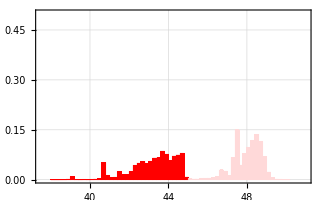

```mathematica
his1=Show[Histogram[WeightedData[M1$1octx[[All,7]],Exp[-M1$1octx[[All,1]]/2]],{38,51,0.2},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M1N1"]},{{0.05,0.98},{10^-3,1}}]],

Histogram[WeightedData[M1$2octx[[All,7]],Exp[-M1$2octx[[All,1]]/2]],{38,51,0.2},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M1N2"]},{{0.05,0.88},{0,1}}]],ImageSize->324,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],PlotRange->{{37.5,51},{10^-5,0.5}},FrameLabel->{tex["\\theta_{23}~[^\\circ]"],None},FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
ticks=FrameTicks/. AbsoluteOptions[his1,FrameTicks];
leftTicks=Map[{#[[1]],"",0.01}&,ticks[[1,1]]];
```

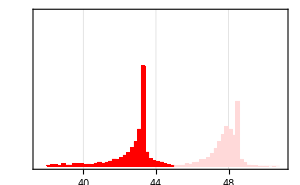

```mathematica
his2=Show[Histogram[WeightedData[M2$1octx[[All,7]],Exp[-M2$1octx[[All,1]]/2]],{38,51,0.2},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M2N1"]},{{0.05,0.98},{10^-4,1}}]],

Histogram[WeightedData[M2$2octx[[All,7]],Exp[-M2$2octx[[All,1]]/2]],{38,51,0.2},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M2N2"]},{{0.05,0.88},{0,1}}]],ImageSize->300,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],PlotRange->{{37.5,51},{10^-5,0.5}},FrameTicks->{{leftTicks,None},{Automatic,None}},FrameLabel->{tex["\\theta_{23}~[^\\circ]"],None}]
```

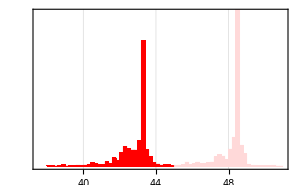

```mathematica
his3=Show[Histogram[WeightedData[M3$1octx[[All,7]],Exp[-M3$1octx[[All,1]]/2]],{38,51,0.2},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M3N1"]},{{0.05,0.98},{10^-4,1}}]],

Histogram[WeightedData[M3$2octx[[All,7]],Exp[-M3$2octx[[All,1]]/2]],{38,51,0.2},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M3N2"]},{{0.05,0.88},{0,1}}]],ImageSize->300,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],PlotRange->{{37.5,51},{10^-5,0.5}},FrameTicks->{{leftTicks,None},{Automatic,None}},FrameLabel->{tex["\\theta_{23}~[^\\circ]"],None}]
```

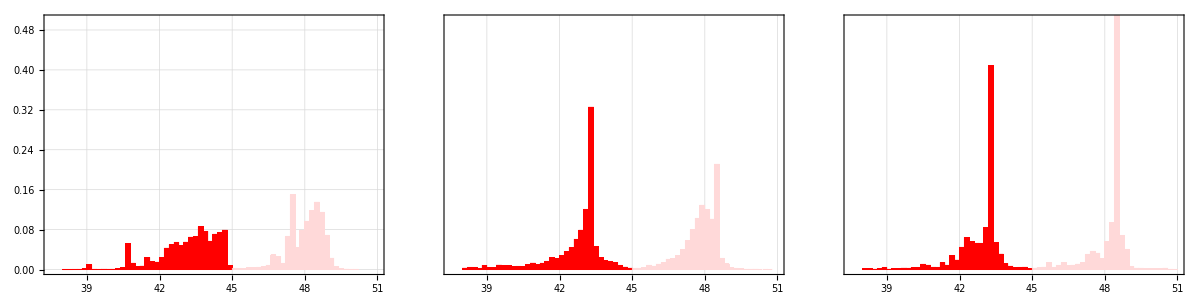

```mathematica
pltall$1=Grid[{{Show[his1,ImagePadding->{{Automatic,Automatic},{64,Automatic}}],
Show[his2,ImagePadding->{{Automatic,Automatic},{70,Automatic}}],
Show[his3,ImagePadding->{{Automatic,Automatic},{70,Automatic}}]}}]
```

## 4. δ distribution

```mathematica
(*
nor11=Normalize[HistogramList[WeightedData[M1$1oct[[All,8]],Exp[-M1$1oct[[All,1]]/2]],{0,360,4}][[2]]/4,Max]&;
nor12=Normalize[HistogramList[WeightedData[M1$2oct[[All,8]],Exp[-M1$2oct[[All,1]]/2]],{0,360,4}][[2]]/4,Max]&;

nor21=Normalize[HistogramList[WeightedData[M2$1oct[[All,8]],Exp[-M2$1oct[[All,1]]/2]],{0,360,4}][[2]]/4,Max]&;
nor22=Normalize[HistogramList[WeightedData[M2$2oct[[All,8]],Exp[-M2$2oct[[All,1]]/2]],{0,360,4}][[2]]/4,Max]&;

nor31=Normalize[HistogramList[WeightedData[M3$1oct[[All,8]],Exp[-M3$1oct[[All,1]]/2]],{0,360,4}][[2]]/4,Max]&;
nor32=Normalize[HistogramList[WeightedData[M3$2oct[[All,8]],Exp[-M3$2oct[[All,1]]/2]],{0,360,4}][[2]]/4,Max]&;*)
```

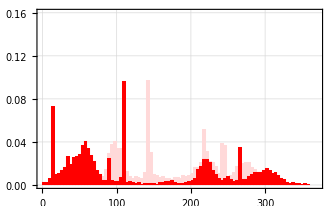

```mathematica
his1=Show[Histogram[WeightedData[M1$2oct[[All,8]],Exp[-M1$2oct[[All,1]]/2]],{0,360,4},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ImageSize->Medium,ChartLegends->Placed[{tex["\\tt M1N2"]},{{0.05,0.88},{10^-4,1}}]],Histogram[WeightedData[M1$1oct[[All,8]],Exp[-M1$1oct[[All,1]]/2]],{0,360,4},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ImageSize->Medium,ChartLegends->Placed[{tex["\\tt M1N1"]},{{0.05,0.98},{10^-4,1}}]],ImageSize->336,PlotRange->{{0,370},{10^-5,0.16}},FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],FrameLabel->{tex["\\delta~[^\\circ]"],None},FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
ticks=FrameTicks/. AbsoluteOptions[his1,FrameTicks];
leftTicks=Map[{#[[1]],"",0.01}&,ticks[[1,1]]];
```

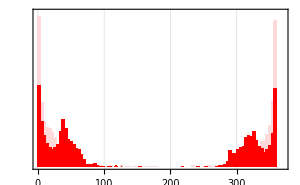

```mathematica
his2=Show[Histogram[WeightedData[M2$2oct[[All,8]],Exp[-M2$2oct[[All,1]]/2]],{0,360,4},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ImageSize->Medium,ChartLegends->Placed[{tex["\\tt M2N2"]},{{0.05,0.88},{10^-3,1}}]],Histogram[WeightedData[M2$1oct[[All,8]],Exp[-M2$1oct[[All,1]]/2]],{0,360,4},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M2N1"]},{{0.05,0.98},{10^-3,1}}]],PlotRange->{{0,370},{10^-5,0.16}},FrameLabel->{tex["\\delta~[^\\circ]"],None},ImageSize->300,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],FrameTicks->{{leftTicks,None},{Automatic,None}}]
```

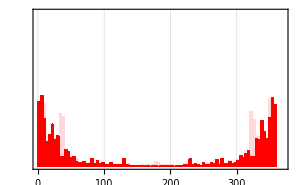

```mathematica
his3=Show[Histogram[WeightedData[M3$2oct[[All,8]],Exp[-M3$2oct[[All,1]]/2]],{0,360,4},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M3N2"]},{{0.05,0.88},{10^-3,1}}]],Histogram[WeightedData[M3$1oct[[All,8]],Exp[-M3$1oct[[All,1]]/2]],{0,360,4},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M3N1"]},{{0.05,0.98},{10^-3,1}}]],PlotRange->{{0,370},{10^-5,0.16}},FrameLabel->{tex["\\delta~[^\\circ]"],None},ImageSize->300,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],FrameTicks->{{leftTicks,None},{Automatic,None}}]
```

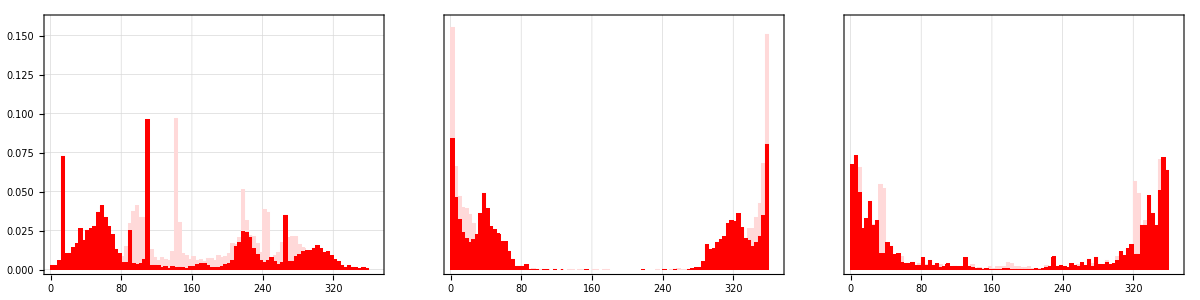

```mathematica
pltall$2=Grid[{{Show[his1,ImagePadding->{{Automatic,Automatic},{66,Automatic}}],
Show[his2,ImagePadding->{{Automatic,Automatic},{67,Automatic}}],
Show[his3,ImagePadding->{{Automatic,Automatic},{67,Automatic}}]}}]
```

#### 3. NMass_1Oct

```mathematica
(*
nor11M1=Normalize[HistogramList[WeightedData[Log10[M1$1oct[[All,2]]],Exp[-M1$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor12M1=Normalize[HistogramList[WeightedData[Log10[M1$2oct[[All,2]]],Exp[-M1$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;

nor21M1=Normalize[HistogramList[WeightedData[Log10[M2$1oct[[All,2]]],Exp[-M2$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor22M1=Normalize[HistogramList[WeightedData[Log10[M2$2oct[[All,2]]],Exp[-M2$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;

nor31M1=Normalize[HistogramList[WeightedData[Log10[M3$1oct[[All,2]]],Exp[-M3$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor32M1=Normalize[HistogramList[WeightedData[Log10[M3$2oct[[All,2]]],Exp[-M3$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
(********************************************************)
nor11M2=Normalize[HistogramList[WeightedData[Log10[M1$1oct[[All,3]]],Exp[-M1$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor12M2=Normalize[HistogramList[WeightedData[Log10[M1$2oct[[All,3]]],Exp[-M1$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;

nor21M2=Normalize[HistogramList[WeightedData[Log10[M2$1oct[[All,3]]],Exp[-M2$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor22M2=Normalize[HistogramList[WeightedData[Log10[M2$2oct[[All,3]]],Exp[-M2$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;

nor31M2=Normalize[HistogramList[WeightedData[Log10[M3$1oct[[All,3]]],Exp[-M3$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor32M2=Normalize[HistogramList[WeightedData[Log10[M3$2oct[[All,3]]],Exp[-M3$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
(********************************************************)
nor11M3=Normalize[HistogramList[WeightedData[Log10[M1$1oct[[All,4]]],Exp[-M1$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor12M3=Normalize[HistogramList[WeightedData[Log10[M1$2oct[[All,4]]],Exp[-M1$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;

nor21M3=Normalize[HistogramList[WeightedData[Log10[M2$1oct[[All,4]]],Exp[-M2$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor22M3=Normalize[HistogramList[WeightedData[Log10[M2$2oct[[All,4]]],Exp[-M2$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;

nor31M3=Normalize[HistogramList[WeightedData[Log10[M3$1oct[[All,4]]],Exp[-M3$1oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;
nor32M3=Normalize[HistogramList[WeightedData[Log10[M3$2oct[[All,4]]],Exp[-M3$2oct[[All,1]]/2]],{4,15.5,0.2}][[2]]/0.2,Max]&;*)
(********************************************************)
```

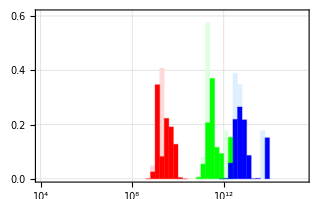

```mathematica
M1m1=Histogram[WeightedData[Log10[M1$1oct[[All,2]]],Exp[-M1$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M1N1"]},{{0.05,0.98},{10^-3,1}}]];
M1m2=Histogram[WeightedData[Log10[M1$1oct[[All,3]]],Exp[-M1$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Green,GridLines->Automatic,Frame->True];
M1m3=Histogram[WeightedData[Log10[M1$1oct[[All,4]]],Exp[-M1$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Blue,GridLines->Automatic,Frame->True];
plt11=Show[{M1m1,M1m2,M1m3}];
M1m1=Histogram[WeightedData[Log10[M1$2oct[[All,2]]],Exp[-M1$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M1N2"]},{{0.05,0.88},{10^-3,1}}]];
M1m2=Histogram[WeightedData[Log10[M1$2oct[[All,3]]],Exp[-M1$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightGreen,GridLines->Automatic,Frame->True];
M1m3=Histogram[WeightedData[Log10[M1$2oct[[All,4]]],Exp[-M1$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightBlue,GridLines->Automatic,Frame->True];
plt12=Show[{M1m1,M1m2,M1m3}];
pltt1=Show[plt12,plt11,PlotRange->{{4,15.5},{0.00001,0.61}},FrameLabel->{tex["M_i ~[\\rm GeV]"],None},ImageSize->322,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],FrameTicks->{{Automatic,None},{{{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"}},None}}]
```

```mathematica
ticks=FrameTicks/. AbsoluteOptions[pltt1,FrameTicks];
leftTicks=Map[{#[[1]],"",0.01}&,ticks[[1,1]]];
```

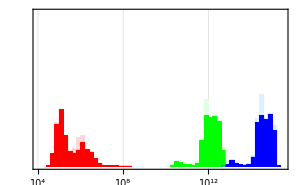

```mathematica
M2m1=Histogram[WeightedData[Log10[M2$1oct[[All,2]]],Exp[-M2$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M2N1"]},{{0.05,0.98},{10^-3,1}}]];
M2m2=Histogram[WeightedData[Log10[M2$1oct[[All,3]]],Exp[-M2$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Green,GridLines->Automatic,Frame->True];
M2m3=Histogram[WeightedData[Log10[M2$1oct[[All,4]]],Exp[-M2$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Blue,GridLines->Automatic,Frame->True];
plt21=Show[{M2m1,M2m2,M2m3}];
M2m1=Histogram[WeightedData[Log10[M2$2oct[[All,2]]],Exp[-M2$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M2N2"]},{{0.05,0.88},{10^-3,1}}]];
M2m2=Histogram[WeightedData[Log10[M2$2oct[[All,3]]],Exp[-M2$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightGreen,GridLines->Automatic,Frame->True];
M2m3=Histogram[WeightedData[Log10[M2$2oct[[All,4]]],Exp[-M2$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightBlue,GridLines->Automatic,Frame->True];
plt22=Show[{M2m1,M2m2,M2m3}];
pltt2=Show[plt22,plt21,PlotRange->{{4,15.5},{0.00001,0.61}},FrameLabel->{tex["M_i ~[\\rm GeV]"],None},ImageSize->300,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],FrameTicks->{{leftTicks,None},{{{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"}},None}}]
```

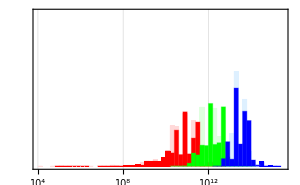

```mathematica
M3m1=Histogram[WeightedData[Log10[M3$1oct[[All,2]]],Exp[-M3$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Red,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M3N1"]},{{0.05,0.98},{10^-3,1}}]];
M3m2=Histogram[WeightedData[Log10[M3$1oct[[All,3]]],Exp[-M3$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Green,GridLines->Automatic,Frame->True];
M3m3=Histogram[WeightedData[Log10[M3$1oct[[All,4]]],Exp[-M3$1oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->Blue,GridLines->Automatic,Frame->True];
plt31=Show[{M3m1,M3m2,M3m3}];
M3m1=Histogram[WeightedData[Log10[M3$2oct[[All,2]]],Exp[-M3$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightRed,GridLines->Automatic,Frame->True,ChartLegends->Placed[{tex["\\tt M3N2"]},{{0.05,0.88},{10^-3,1}}]];
M3m2=Histogram[WeightedData[Log10[M3$2oct[[All,3]]],Exp[-M3$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightGreen,GridLines->Automatic,Frame->True];
M3m3=Histogram[WeightedData[Log10[M3$2oct[[All,4]]],Exp[-M3$2oct[[All,1]]/2]],{4,15.5,0.2},"Probability",ChartStyle->LightBlue,GridLines->Automatic,Frame->True];
plt32=Show[{M3m1,M3m2,M3m3}];
pltt3=Show[plt32,plt31,PlotRange->{{4,15.5},{0.00001,0.61}},FrameLabel->{tex["M_i ~[\\rm GeV]"],None},ImageSize->300,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[18,Black],FrameTicks->{{leftTicks,None},{{{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"}},None}}]
```

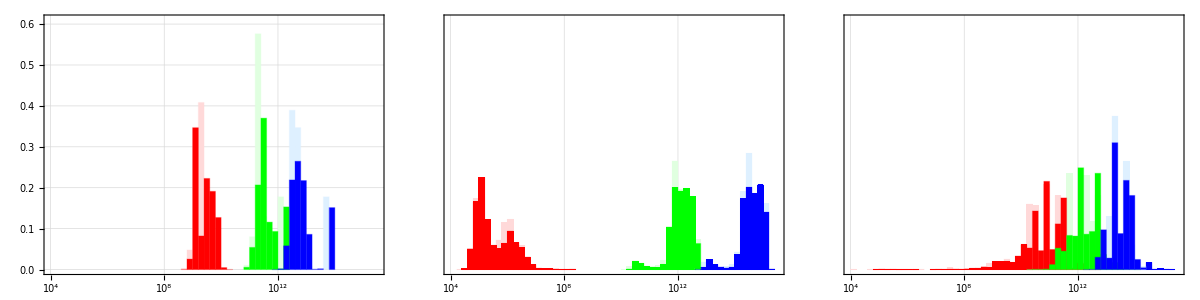

```mathematica
pltall$3=Grid[{{Show[pltt1,ImagePadding->{{Automatic,Automatic},{60,Automatic}}],
Show[pltt2,ImagePadding->{{Automatic,Automatic},{70,Automatic}}],
Show[pltt3,ImagePadding->{{Automatic,Automatic},{70,Automatic}}]}},Spacings->{0.2,0.2}]
```

```mathematica
plot$all=Grid[{{pltall$1},{pltall$2},{pltall$3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"weight.pdf"}],plot$all//Rasterize]
```

/Users/admin_phy/Desktop/GUT_Plot/Final/weight.pdf